# Pendolo invertito

```mathematica
v2 = (x'[t] + l θ'[t]*Cos[θ[t]])^2 + ( l θ'[t]*Sin[θ[t]])^2;
T = 1/2 *M*x'[t]^2       + 1/2* m*v2    + 1/2*(J - m l^2)*θ'[t]^2 
V = m*g*l*Cos[θ[t]];
L = T - V;

T //  TraditionalForm

e1 =D[D[L, x'[t]], t] - D[L, x[t]] == +u[t]
e2 = D[D[L, θ'[t]], t] - D[L, θ[t]] ==0 //Simplify

motionEquations = Simplify[Solve[e1 && e2, {x''[t], θ''[t]}]][[1]];

(*https://www.12000.org/my_notes/cart_motion/report.htm*)
Simplify[Solve[e1, { x''[t]}]][[1]] //TraditionalForm 
Simplify[Solve[e2, { θ''[t]}]][[1]] //TraditionalForm

motionEquations[[1, 2]]//Simplify//TraditionalForm
motionEquations[[2, 2]] //Simplify // TraditionalForm
```

1/2 M x'[t]^2+1/2 (J-l^2 m) θ'[t]^2+1/2 m (l^2 Sin[θ[t]]^2 θ'[t]^2+(x'[t]+l Cos[θ[t]] θ'[t])^2)

1/2 (J-l^2 m) (θ'(t))^2+1/2 m (l^2 (θ'(t))^2 sin^2(θ(t))+(l θ'(t) cos(θ(t))+x'(t))^2)+1/2 M (x'(t))^2

M x''[t]+m (-l Sin[θ[t]] θ'[t]^2+x''[t]+l Cos[θ[t]] θ''[t])==u[t]

g l m Sin[θ[t]]==l m Cos[θ[t]] x''[t]+J θ''[t]

{x''(t)→(-l m θ''(t) cos(θ(t))+l m (θ'(t))^2 sin(θ(t))+u(t))/(m+M)}

{θ''(t)→(l m (g sin(θ(t))-cos(θ(t)) x''(t)))/J}

(l m sin(θ(t)) (J (θ'(t))^2-g l m cos(θ(t)))+J u(t))/(J (m+M)-l^2 m^2 cos^2(θ(t)))

(l m (sin(θ(t)) (l m (θ'(t))^2 cos(θ(t))-g (m+M))+u(t) cos(θ(t))))/(l^2 m^2 cos^2(θ(t))-J (m+M))

## Create space state model

```mathematica
ssm = StateSpaceModel[
{e1, e2},
{
x[t],
	{x'[t], 0},
	{θ[t], 0},
	{θ'[t], 0}
},
{u[t]},
{θ[t], x[t], θ'[t]},
t
]  //Simplify
A = ssm[[1, 1]];
B = ssm[[1, 2]]//Flatten;
```

0100000-(g l^2 m^2)/(J (m+M)+l^2 m (m+2 M))0(J+2 l^2 m)/(J (m+M)+l^2 m (m+2 M))0001000(g l m (m+M))/(J (m+M)+l^2 m (m+2 M))0-(l m)/(J (m+M)+l^2 m (m+2 M))001001000000010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1341FalseFalseFalseAutomaticNone,{{x[t],0},x_1,{θ[t],0},x_2},{{u[t],0}},Automatic,t

```mathematica
Solve[({B, A.B, A.A.B, A.A.A.B} //Det) == 0]
RowReduce[{B, A.B, A.A.B, A.A.A.B}] //MatrixForm
```

{{g→0},{l→0},{m→0}}

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Q = ResourceFunction["HessianMatrix"][T-V, {x[t], x'[t],θ[t], θ'[t]}]  /. {x[t] -> 0, x'[t] ->0, θ[t] -> 0, θ'[t] -> 0}//MatrixForm
(ResourceFunction["HessianMatrix"][T-V, {x[t], x'[t],θ[t], θ'[t]}] /. {x[t] -> 0, x'[t] ->0, θ[t] -> 0, θ'[t] -> 0} )//. params //Eigenvalues
(*Qmatrix = DiagonalMatrix[{1, 0, 0, 0}];
Rmatrix = DiagonalMatrix[{.005}];
Klqr = LQRegulatorGains[ssm /. params, {Qmatrix, Rmatrix}]*)
```

(0 | 0 | 0 | 0
0 | m+M | 0 | l m
0 | 0 | g l m | 0
0 | l m | 0 | J)

{0.5586,0.334707,-0.009707,0.}

## Simulation without control

```mathematica
params = {
g ->9.8,
l -> .38,
m -> .15,
M -> .175,
β ->0,
J->0
};



linearisedEquations = Thread[{θ'[t], θ''[t],  x'[t], x''[t]} == A.Transpose[{θ[t], θ'[t],  x[t], x'[t]} ]];
l1 = linearisedEquations[[2]];
l2 = linearisedEquations[[4]];
l1 // Simplify // TraditionalForm
l2 // Simplify// TraditionalForm
```

θ''(t)==(g l^2 m^2 x(t))/(l^2 m^2-J (m+M))

(g l m (m+M) x(t))/(l^2 m^2-J (m+M))+x''(t)==0

{θ''[t]==-(g l^2 m^2 x[t])/(J (m+M)+l^2 m (m+2 M)),x''[t]==(g l m (m+M) x[t])/(J (m+M)+l^2 m (m+2 M)),x[0]==x'[0]==θ'[0]==0,θ[0]==1}

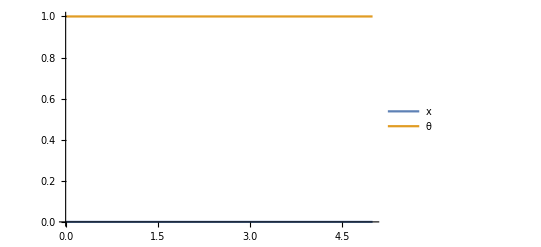

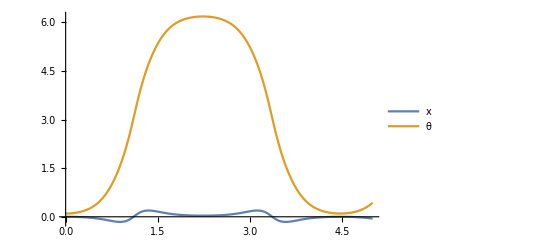

```mathematica
eqnsLinear = {
l1, l2,
x[0] == x'[0] == θ'[0] == 0, θ[0] == 1
} 



eqnsNonLinear = {
e1, e2,
x[0] == x'[0] == θ'[0] == 0, θ[0] ==.1
} /. params /. u[t]->0;



T=5;
solsL =  NDSolve[eqnsLinear, {x, θ}, {t, 0, T}];
solsN =  NDSolve[eqnsNonLinear, {x, θ}, {t, 0, T}];

Plot[Evaluate[{x[t], θ[t]} /.  solsL], {t, 0, T}, PlotLegends->{x, θ}]
Plot[Evaluate[{x[t], θ[t]} /.  solsN], {t, 0, T},PlotLegends->{x, θ}]
```

## Pole placement

```mathematica
p = {-1, -1.1, -1.2, -1.3};
K = StateFeedbackGains[ssm,p] /. params;

(*θ θ'x x'*)
Qmatrix = DiagonalMatrix[{1, .0001, .1, .0001}];
Rmatrix = DiagonalMatrix[{.005}];
Klqr = LQRegulatorGains[ssm /. params, {Qmatrix, Rmatrix}]

K // MatrixForm
(A-B.K) /. params //Eigenvalues
```

{{-14.1421,-10.6659,-42.5946,-11.5894}}

(-0.0332694 | -0.116831 | -4.71318 | -0.962791)

Dot::dotsh: Tensors {0,(J+2 l^2 m)/(J (m+M)+l^2 m (m+2 M)),0,-(l m)/(J (m+M)+l^2 m (m+2 M))} and {{-0.0332694,-0.116831,-4.71318,-0.962791}} have incompatible shapes.

Dot::dotsh: Tensors {0,4.,0,-5.26316} and {{-0.0332694,-0.116831,-4.71318,-0.962791}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{Root[-19.7032 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}}-39.4063 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}} #1+(-16.7632+15.8232 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}}) #1^2+4 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}} #1^3+#1^4&,1],Root[-19.7032 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}}-39.4063 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}} #1+(-16.7632+15.8232 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}}) #1^2+4 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}} #1^3+#1^4&,2],Root[-19.7032 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}}-39.4063 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}} #1+(-16.7632+15.8232 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}}) #1^2+4 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}} #1^3+#1^4&,3],Root[-19.7032 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}}-39.4063 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}} #1+(-16.7632+15.8232 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}}) #1^2+4 {0,4.,0,-5.26316}.{{-0.0332694,-0.116831,-4.71318,-0.962791}} #1^3+#1^4&,4]}

```mathematica
discrete = ToDiscreteTimeModel[ssm, 0.02];
```

```mathematica
qqMatrix =  DiagonalMatrix[{1, .01, 1, .0001}];
```

```mathematica
Klqrd = LQRegulatorGains[discrete /. params, {qqMatrix, Rmatrix}]
```

DiscreteRiccatiSolve::nonnum: DiscreteRiccatiSolve has received a matrix with non-numerical elements.

LQRegulatorGains[0.+1./(1.+0.0000181545/(0.003249-0.325 J))+(0.01 (0.-1. (0.+0.00181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))0.+0.02/(1.+0.0000181545/(0.003249-0.325 J))0.0.0.+0.00057/((1.+0.0000181545/(0.003249-0.325 J)) (0.003249-0.325 J))0.+(1. (0.-1. (0.+0.00181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))-0.00181545/((1.+0.0000181545/(0.003249-0.325 J)) (0.003249-0.325 J))0.+1./(1.+0.0000181545/(0.003249-0.325 J))-0.0000181545/((1.+0.0000181545/(0.003249-0.325 J)) (0.003249-0.325 J))0.0.0.+0.057/((1.+0.0000181545/(0.003249-0.325 J)) (0.003249-0.325 J))0.+(1. (0.+(3.18402×10^-6)/(0.003249-0.325 J)))/(1.+0.0000181545/(0.003249-0.325 J))+(0.01 (0.+0.000318402/(0.003249-0.325 J)))/(1.+0.0000181545/(0.003249-0.325 J))0.+(1. (0.+(3.18402×10^-8)/(0.003249-0.325 J)))/(1.+0.0000181545/(0.003249-0.325 J))+(0.01 (0.+(3.18402×10^-6)/(0.003249-0.325 J)))/(1.+0.0000181545/(0.003249-0.325 J))0.+(1. (0.+1. (1.+0.0000181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))0.+(1. (0.+0.01 (1.+0.0000181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))+(0.01 (0.+1. (1.+0.0000181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))(0.057 (0.+(3.18402×10^-8)/(0.003249-0.325 J)))/((1.+0.0000181545/(0.003249-0.325 J)) (0.003249-0.325 J))+((0.+0.01 (1.+0.0000181545/(0.003249-0.325 J))) J)/((1.+0.0000181545/(0.003249-0.325 J)) (-0.003249+0.325 J))0.+(1. (0.+0.000318402/(0.003249-0.325 J)))/(1.+0.0000181545/(0.003249-0.325 J))+0.000318402/((1.+0.0000181545/(0.003249-0.325 J)) (0.003249-0.325 J))0.+(1. (0.+(3.18402×10^-6)/(0.003249-0.325 J)))/(1.+0.0000181545/(0.003249-0.325 J))+(3.18402×10^-6)/((1.+0.0000181545/(0.003249-0.325 J)) (0.003249-0.325 J))0.0.+(1. (0.+1. (1.+0.0000181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))0.+(0.057 (0.+(3.18402×10^-6)/(0.003249-0.325 J)))/((1.+0.0000181545/(0.003249-0.325 J)) (0.003249-0.325 J))+((0.+1. (1.+0.0000181545/(0.003249-0.325 J))) J)/((1.+0.0000181545/(0.003249-0.325 J)) (-0.003249+0.325 J))0.+0.02/(1.+0.0000181545/(0.003249-0.325 J))0.+0.0002/(1.+0.0000181545/(0.003249-0.325 J))0.0.0.+(0.0285 (0.+0.0002/(1.+0.0000181545/(0.003249-0.325 J))))/(0.003249-0.325 J)0.+(0.02 (0.+(3.18402×10^-6)/(0.003249-0.325 J)))/(1.+0.0000181545/(0.003249-0.325 J))0.+(0.02 (0.+(3.18402×10^-8)/(0.003249-0.325 J)))/(1.+0.0000181545/(0.003249-0.325 J))0.+(0.02 (0.+1. (1.+0.0000181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))0.+(0.02 (0.+0.01 (1.+0.0000181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))(0.0285 (0.+(0.02 (0.+(3.18402×10^-8)/(0.003249-0.325 J)))/(1.+0.0000181545/(0.003249-0.325 J))))/(0.003249-0.325 J)+((0.+(0.02 (0.+0.01 (1.+0.0000181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))) J)/(2 (-0.003249+0.325 J))0.+(0.02 (0.-1. (0.+0.00181545/(0.003249-0.325 J))))/(1.+0.0000181545/(0.003249-0.325 J))0.+0.02/(1.+0.0000181545/(0.003249-0.325 J))0.0.0.+(0.0285 (0.+0.02/(1.+0.0000181545/(0.003249-0.325 J))))/(0.003249-0.325 J)0.02StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1341FalseFalseFalseAutomaticNone,{{θ[k],0},x_1,{x[k],0},x_2},{{u[k],0}},Automatic,k,{{{1.,0.,0.,0.},{0.,0.01,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.0001}},{{0.005}}}]

## Apply control

```mathematica
s[t_] = {θ[t], θ'[t], x[t],  x'[t]};
controlLQR = {u[t] -> -Klqr.(s[t])};


eqnsControlLQR = {
	e1, e2,
	x[0] ==.05, x'[0] == θ'[0] == 0, θ[0] ==.05
} /. params /. controlLQR
T = 4;
solsN =  NDSolve[eqnsControlLQR, {x, θ}, {t, 0, T}];
powerLQR =u[t]^2 /. controlLQR /. solsN;

lqrPlot = Plot[Evaluate[{x[t], θ[t], u[t]/.controlLQR} /.  solsN], {t, 0,T},PlotLegends->{"x (m)", "θ (rad)", "u (N)"}, PlotRange->{-.3, .3}, AxesLabel->{"t (s}"}]
NIntegrate[powerLQR, {t, 0, T}]
```

{0.175 x''[t]+0.15 (-0.38 Sin[θ[t]] θ'[t]^2+x''[t]+0.38 Cos[θ[t]] θ''[t])=={-7.69875 x[t]-14.1421 θ[t]-0.947448 x'[t]-5.60644 θ'[t]},0.5586 Sin[θ[t]]==0.057 Cos[θ[t]] x''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05}

NDSolve::ndfdmc: Computed derivatives do not have dimensionality consistent with the initial conditions.

ReplaceAll::reps: {NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])=={-7.69875 x[«1»]-14.1421 θ[«1»]-0.947448 («1»)^(«1»)[«1»]-5.60644 («1»)^(«1»)[«1»]},0.5586 Sin[θ[t]]==0.057 Cos[θ[t]] x''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.175 x''[0.0000817143]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])=={-7.69875 x[«1»]-14.1421 θ[«1»]-0.947448 («1»)^(«1»)[«1»]-5.60644 («1»)^(«1»)[«1»]},0.5586 Sin[θ[0.0000817143]]==0.057 Cos[θ[0.0000817143]] x''[0.0000817143],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{0.0000817143,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.175 x''[0.0000817143]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])=={-7.69875 x[«1»]-14.1421 θ[«1»]-0.947448 («1»)^(«1»)[«1»]-5.60644 («1»)^(«1»)[«1»]},0.5586 Sin[θ[0.0000817143]]==0.057 Cos[θ[0.0000817143]] x''[0.0000817143],x[0.]==0.05,x'[0.]==θ'[0.]==0.,θ[0.]==0.05},{x,θ},{0.0000817143,0.,4.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0817144 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndfdmc: Computed derivatives do not have dimensionality consistent with the initial conditions.

ReplaceAll::reps: {NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])=={-7.69875 x[«1»]-14.1421 θ[«1»]-0.947448 («1»)^(«1»)[«1»]-5.60644 («1»)^(«1»)[«1»]},0.5586 Sin[θ[t]]==0.057 Cos[θ[t]] x''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndfdmc: Computed derivatives do not have dimensionality consistent with the initial conditions.

ReplaceAll::reps: {NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])=={-7.69875 x[«1»]-14.1421 θ[«1»]-0.947448 («1»)^(«1»)[«1»]-5.60644 («1»)^(«1»)[«1»]},0.5586 Sin[θ[t]]==0.057 Cos[θ[t]] x''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand {(-7.69875 x[t]-14.1421 θ[t]-0.947448 x'[t]-5.60644 θ'[t])^2}/.NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])=={-7.69875 x[«1»]-14.1421 θ[«1»]-0.947448 («1»)^(«1»)[«1»]-5.60644 («1»)^(«1»)[«1»]},0.5586 Sin[θ[t]]==0.057 Cos[θ[t]] x''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4}}.

NIntegrate[powerLQR,{t,0,T}]

```mathematica
controlPID =  {u[t] -> 15*s[t][[1]]  + 1300*s[t][[2]] + 2*s[t][[3]] + 1000*s[t][[4]] };
eqnsControlPID = {
e1, e2,
x[0] ==.05, x'[0] == θ'[0] == 0, θ[0] ==.05
} /. params /. controlPID;
T = 4;
solsN =  NDSolve[eqnsControlPID, {x, θ}, {t, 0, T}];
powerPID =u[t]^2 /. controlPID /. solsN;

pidPlot = Plot[Evaluate[{x[t], θ[t], u[t]/.controlPID} /.  solsN], {t, 0,T},PlotLegends->{"x (m)", "θ (rad)", "u (N)"}, PlotRange->{-.3, .3}, AxesLabel->{"t (s}"}]
NIntegrate[powerPID, {t, 0, T}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==2 x[t]+15 θ[t]+1000 x'[t]+1300 θ'[t],0.5586 Sin[θ[t]]==0.057 Cos[θ[«1»]] x''[t]+J θ''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.175 x''[0.0000817143]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==2 x[0.0000817143]+15 θ[0.0000817143]+1000 x'[0.0000817143]+1300 θ'[0.0000817143],0.5586 Sin[θ[0.0000817143]]==0.057 Cos[θ[«1»]] x''[0.0000817143]+J θ''[0.0000817143],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{0.0000817143,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.175 x''[0.0000817143]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==2. x[0.0000817143]+15. θ[0.0000817143]+1000. x'[0.0000817143]+1300. θ'[0.0000817143],0.5586 Sin[θ[0.0000817143]]==0.057 Cos[θ[«1»]] x''[0.0000817143]+J θ''[0.0000817143],x[0.]==0.05,x'[0.]==θ'[0.]==0.,θ[0.]==0.05},{x,θ},{0.0000817143,0.,4.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0817144 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==2 x[t]+15 θ[t]+1000 x'[t]+1300 θ'[t],0.5586 Sin[θ[t]]==0.057 Cos[θ[«1»]] x''[t]+J θ''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==2 x[t]+15 θ[t]+1000 x'[t]+1300 θ'[t],0.5586 Sin[θ[t]]==0.057 Cos[θ[«1»]] x''[t]+J θ''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand (2 x[t]+15 θ[t]+1000 x'[t]+1300 θ'[t])^2/.NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==2 x[t]+15 θ[t]+1000 x'[t]+1300 θ'[t],0.5586 Sin[θ[t]]==0.057 Cos[θ[«1»]] x''[t]+J θ''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4}}.

NIntegrate[powerPID,{t,0,T}]

# Altri calcoli

# Swingup control

```mathematica
state = {
x'[t] == v[t],
v'[t] == (x''[t] /. motionEquations (*/. M -> (m - m*b)/b*) // Simplify),
θ'[t] == ω[t],
ω'[t] == (θ''[t] /. motionEquations (*/. M -> (m - m*b)/b*) // Simplify)
}



{x'[t]==v[t],v'[t]==(-8 u[t]+2 m Sin[θ[t]] (3 g Cos[θ[t]]-2 l θ'[t]^2))/(-5 m-8 M+3 m Cos[2 θ[t]]),θ'[t]==ω[t],ω'[t]==(6 Cos[θ[t]] u[t]+3 Sin[θ[t]] (-2 g (m+M)+l m Cos[θ[t]] θ'[t]^2))/(l (-4 (m+M)+3 m Cos[θ[t]]^2))}
```

{x'[t]==v[t],v'[t]==(J u[t]+l m Sin[θ[t]] (-g l m Cos[θ[t]]+J θ'[t]^2))/(J (m+M)-l^2 m^2 Cos[θ[t]]^2),θ'[t]==ω[t],ω'[t]==(l m (Cos[θ[t]] u[t]+Sin[θ[t]] (-g (m+M)+l m Cos[θ[t]] θ'[t]^2)))/(-J (m+M)+l^2 m^2 Cos[θ[t]]^2)}

{x'[t]==v[t],v'[t]==(-8 u[t]+2 m Sin[θ[t]] (3 g Cos[θ[t]]-2 l θ'[t]^2))/(-5 m-8 M+3 m Cos[2 θ[t]]),θ'[t]==ω[t],ω'[t]==(6 Cos[θ[t]] u[t]+3 Sin[θ[t]] (-2 g (m+M)+l m Cos[θ[t]] θ'[t]^2))/(l (-4 (m+M)+3 m Cos[θ[t]]^2))}

```mathematica
stateEquations = state /.Equal->Rule /. {x'[t] -> v[t], θ'[t] -> ω[t]};
```

```mathematica
jacobian = D[stateEquations[[All, 2]], {{x[t], v[t], θ[t], ω[t], u[t]}}]//Simplify;
```

```mathematica
jacobian /. {θ[t]-> 0, ω[t] -> 0, v[t]->0} // Simplify //MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | (g l^2 m^2)/(l^2 m^2-J (m+M)) | 0 | J/(-l^2 m^2+J (m+M))
0 | 0 | 0 | 1 | 0
0 | 0 | -(g l m (m+M))/(l^2 m^2-J (m+M)) | 0 | (l m)/(l^2 m^2-J (m+M)))

```mathematica
A = (jacobian /. {θ[t]-> Pi, ω[t] -> 0, v[t]->0})[[All, 1;;4]] // Simplify
```

{{0,1,0,0},{0,0,(g l^2 m^2)/(l^2 m^2-J (m+M)),0},{0,0,0,1},{0,0,(g l m (m+M))/(l^2 m^2-J (m+M)),0}}

```mathematica
B = (jacobian /. {θ[t]-> Pi, ω[t] -> 0, v[t]->0})[[All, 5]] //Transpose // Simplify
```

{0,J/(-l^2 m^2+J (m+M)),0,(l m)/(-l^2 m^2+J (m+M))}

```mathematica
Solve[({B, A.B, A.A.B, A.A.A.B} // Det) == 0]
```

{{g→0},{l→0},{m→0}}

```mathematica
A
```

{{0,1,0,0},{0,0,(g l^2 m^2)/(l^2 m^2-J (m+M)),0},{0,0,0,1},{0,0,(g l m (m+M))/(l^2 m^2-J (m+M)),0}}

```mathematica
((A //Eigenvalues) /. params)[[3]] / Pi
```

-((0.+0.135626 ⅈ) √(-0.003249+0.325 J))/(0.003249-0.325 J)

```mathematica
AD= MatrixExp[(A/.params)0.02] //MatrixForm
```

(1. | 0.02 | 0.0876923 ⅇ^(-(1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) (1.-2. ⅇ^((1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J))+1. ⅇ^((2. √(235936.-2.36009×10^7 J))/(-3249.+325000. J))) | -(0.00350769 ⅇ^(-(1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) (-1624.5+1624.5 ⅇ^((2. √(235936.-2.36009×10^7 J))/(-3249.+325000. J))+1. ⅇ^((1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) √(235936.-2.36009×10^7 J)+162500. J-162500. ⅇ^((2. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) J))/(√(235936.-2.36009×10^7 J))
0. | 1. | -(318.402 ⅇ^(-(1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) (-1.+1. ⅇ^((2. √(235936.-2.36009×10^7 J))/(-3249.+325000. J))))/(√(235936.-2.36009×10^7 J)) | -0.175385 ⅇ^(-(1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) (-0.5+1. ⅇ^((1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J))-0.5 ⅇ^((2. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)))
0. | 0. | 0.5 ⅇ^(-(1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) (1.+1. ⅇ^((2. √(235936.-2.36009×10^7 J))/(-3249.+325000. J))) | -0.000137707 ⅇ^(-(1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) (-1.+1. ⅇ^((2. √(235936.-2.36009×10^7 J))/(-3249.+325000. J))) √(235936.-2.36009×10^7 J)
0. | 0. | -(1815.45 ⅇ^(-(1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) (-1.+1. ⅇ^((2. √(235936.-2.36009×10^7 J))/(-3249.+325000. J))))/(√(235936.-2.36009×10^7 J)) | 0.5 ⅇ^(-(1. √(235936.-2.36009×10^7 J))/(-3249.+325000. J)) (1.+1. ⅇ^((2. √(235936.-2.36009×10^7 J))/(-3249.+325000. J))))

```mathematica
AD = A+IdentityMatrix[4]*0.02;
BD =( B*0.02 //Transpose)[[1]]
```

0.

```mathematica
RealDigits[BD]
```

{{0},-323}

```mathematica
{BD, AD.BD, AD.AD.BD, AD.AD.AD.BD} //MatrixRank
```

MatrixRank::matrix: Argument «1» at position 1 is not a non-empty rectangular matrix.

MatrixRank[{0.,{{0.02,1.,0.,0.},{0.,0.02,0.+(g l^2 m^2)/(l^2 m^2-J (m+M)),0.},{0.,0.,0.02,1.},{0.,0.,0.+(g l m (m+M))/(l^2 m^2-J (m+M)),0.02}}.0.,{{0.0004,0.04,0.+1. (0.+(g l^2 m^2)/(l^2 m^2-J (m+M))),0.},{0.,0.0004,0.+0.04 (0.+(g l^2 m^2)/(l^2 m^2-J (m+M))),0.+1. (0.+(g l^2 m^2)/(l^2 m^2-J (m+M)))},{0.,0.,0.0004+1. (0.+(g l m (m+M))/(l^2 m^2-J (m+M))),0.04},{0.,0.,0.+0.04 (0.+(g l m (m+M))/(l^2 m^2-J (m+M))),0.0004+1. (0.+(g l m (m+M))/(l^2 m^2-J (m+M)))}}.0.,{{8.×10^-6,0.0012,0.+0.04 (0.+(g l^2 m^2)/(l^2 m^2-J (m+M)))+0.02 (0.+1. (0.+(g l^2 m^2)/(l^2 m^2-J (m+M)))),0.+1. (0.+1. (0.+(g l^2 m^2)/(l^2 m^2-J (m+M))))},{0.,8.×10^-6,0.+0.0004 (0.+(g l^2 m^2)/(l^2 m^2-J (m+M)))+0.02 (0.+0.04 (0.+(g l^2 m^2)/(l^2 m^2-J (m+M))))+(0.+(g l m (m+M))/(l^2 m^2-J (m+M))) (0.+1. (0.+(g l^2 m^2)/(l^2 m^2-J (m+M)))),0.+1. (0.+0.04 (0.+(g l^2 m^2)/(l^2 m^2-J (m+M))))+0.02 (0.+1. (0.+(g l^2 m^2)/(l^2 m^2-J (m+M))))},{0.,0.,0.+0.04 (0.+(g l m (m+M))/(l^2 m^2-J (m+M)))+0.02 (0.0004+1. (0.+(g l m (m+M))/(l^2 m^2-J (m+M)))),0.0008+1. (0.0004+1. (0.+(g l m (m+M))/(l^2 m^2-J (m+M))))},{0.,0.,0.+0.02 (0.+0.04 (0.+(g l m (m+M))/(l^2 m^2-J (m+M))))+(0.+(g l m (m+M))/(l^2 m^2-J (m+M))) (0.0004+1. (0.+(g l m (m+M))/(l^2 m^2-J (m+M)))),0.+1. (0.+0.04 (0.+(g l m (m+M))/(l^2 m^2-J (m+M))))+0.02 (0.0004+1. (0.+(g l m (m+M))/(l^2 m^2-J (m+M))))}}.0.}]

```mathematica
setpoint = {0, 0, 0, 0};(*Make sure to change setpoint in eqnsControl as well*)
s[t_] = {θ[t], θ'[t], x[t],  x'[t]};
controlLQR = {u[t] -> -Klqr.(s[t]-setpoint)};


eqnsControlLQR = {
e1, e2,
x[0] ==.05, x'[0] == θ'[0] == 0, θ[0] ==.05
} /. params /. controlLQR;
T = 4;
solsN =  NDSolve[eqnsControlLQR, {x, θ}, {t, 0, T}];
powerLQR =u[t]^2 /. controlLQR /. solsN;

lqrPlot = Plot[Evaluate[{x[t], θ[t], u[t]/.controlLQR} /.  solsN], {t, 0,T},PlotLegends->{"x (m)", "θ (rad)", "u (N)"}, PlotRange->{-.3, .3}, AxesLabel->{"t (s}"}]
NIntegrate[powerLQR, {t, 0, T}]
```

RiccatiSolve::nonnum: RiccatiSolve has received a matrix with non-numerical elements.

NDSolve::underdet: There are more dependent variables, {u[t],x[t],θ[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==-LQRegulatorGains[StateSpaceModel[«6»],{«2»}].{θ[«1»],(«1»)^(«1»)[«1»],x[«1»],(«1»)^(«1»)[«1»]},0.5586 Sin[θ[t]]==0.057 Cos[θ[«1»]] x''[t]+J θ''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StateSpaceModel::nonopt: Options expected (instead of 0.0000817143) beyond position 4 in StateSpaceModel[{{{0,1,0,0},{-0.181545/(0.003249+Times[«2»]),0,0,0},{0,0,0,1},{0.0318402/(0.003249+Times[«2»]),0,0,0}},{{0},{0.057/(0.003249+Times[«2»])},{0},{J/(-0.003249+Times[«2»])}},{{1,0,0,0},{0,0,1,0},{0,1,0,0}},{{0},{0},{0}}},{{θ[0.0000817143],0},Automatic,{x[0.0000817143],0},Automatic},{{u[0.0000817143],0}},Automatic,0.0000817143,SamplingPeriod→None]. An option must be a rule or a list of rules.

Control`AffineModelUtilitiesDump`fn::ivar: 0.0000817143 is not a valid variable.

StateSpaceModel::nonopt: Options expected (instead of 0.0000817143) beyond position 4 in StateSpaceModel[{{{0,1,0,0},{-0.181545/(0.003249+Times[«2»]),0,0,0},{0,0,0,1},{0.0318402/(0.003249+Times[«2»]),0,0,0}},{{0},{0.057/(0.003249+Times[«2»])},{0},{J/(-0.003249+Times[«2»])}},{{1,0,0,0},{0,0,1,0},{0,1,0,0}},{{0},{0},{0}}},{{θ[0.0000817143],0},Automatic,{x[0.0000817143],0},Automatic},{{u[0.0000817143],0}},Automatic,0.0000817143,SamplingPeriod→None]. An option must be a rule or a list of rules.

Control`AffineModelUtilitiesDump`fn::ivar: 0.0000817143 is not a valid variable.

NDSolve::dsvar: 0.0000817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.175 x''[0.0000817143]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==-LQRegulatorGains[StateSpaceModel[«6»],{«2»}].{θ[«1»],(«1»)^(«1»)[«1»],x[«1»],(«1»)^(«1»)[«1»]},0.5586 Sin[θ[0.0000817143]]==0.057 Cos[θ[«1»]] x''[0.0000817143]+J θ''[0.0000817143],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{0.0000817143,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StateSpaceModel::nonopt: Options expected (instead of 0.0000817143) beyond position 4 in StateSpaceModel[{{{0.,1.,0.,0.},{-0.181545/(0.003249+Times[«2»]),0.,0.,0.},{0.,0.,0.,1.},{0.0318402/(0.003249+Times[«2»]),0.,0.,0.}},{{0.},{0.057/(0.003249+Times[«2»])},{0.},{J/(-0.003249+Times[«2»])}},{{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,1.,0.,0.}},{{0.},{0.},{0.}}},{{θ[0.0000817143],0.},Automatic,{x[0.0000817143],0.},Automatic},{{u[0.0000817143],0.}},Automatic,0.0000817143,SamplingPeriod→None]. An option must be a rule or a list of rules.

General::stop: Further output of StateSpaceModel::nonopt will be suppressed during this calculation.

Control`AffineModelUtilitiesDump`fn::ivar: 0.0000817143 is not a valid variable.

General::stop: Further output of Control`AffineModelUtilitiesDump`fn::ivar will be suppressed during this calculation.

NDSolve::dsvar: 0.0000817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.175 x''[0.0000817143]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==-1. LQRegulatorGains[StateSpaceModel[«6»],{«2»}].{θ[«1»],(«1»)^(«1»)[«1»],x[«1»],(«1»)^(«1»)[«1»]},0.5586 Sin[θ[0.0000817143]]==0.057 Cos[θ[«1»]] x''[0.0000817143]+J θ''[0.0000817143],x[0.]==0.05,x'[0.]==θ'[0.]==0.,θ[0.]==0.05},{x,θ},{0.0000817143,0.,4.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0817144 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

RiccatiSolve::nonnum: RiccatiSolve has received a matrix with non-numerical elements.

NDSolve::underdet: There are more dependent variables, {u[t],x[t],θ[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==-LQRegulatorGains[StateSpaceModel[«6»],{«2»}].{θ[«1»],(«1»)^(«1»)[«1»],x[«1»],(«1»)^(«1»)[«1»]},0.5586 Sin[θ[t]]==0.057 Cos[θ[«1»]] x''[t]+J θ''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

RiccatiSolve::nonnum: RiccatiSolve has received a matrix with non-numerical elements.

NDSolve::underdet: There are more dependent variables, {u[t],x[t],θ[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{0.175 x''[t]+0.15 (Times[«3»]+(«1»)^(«1»)[«1»]+Times[«3»])==-LQRegulatorGains[StateSpaceModel[«6»],{«2»}].{θ[«1»],(«1»)^(«1»)[«1»],x[«1»],(«1»)^(«1»)[«1»]},0.5586 Sin[θ[t]]==0.057 Cos[θ[«1»]] x''[t]+J θ''[t],x[0]==0.05,x'[0]==θ'[0]==0,θ[0]==0.05},{x,θ},{t,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4}}.

NIntegrate[powerLQR,{t,0,T}]